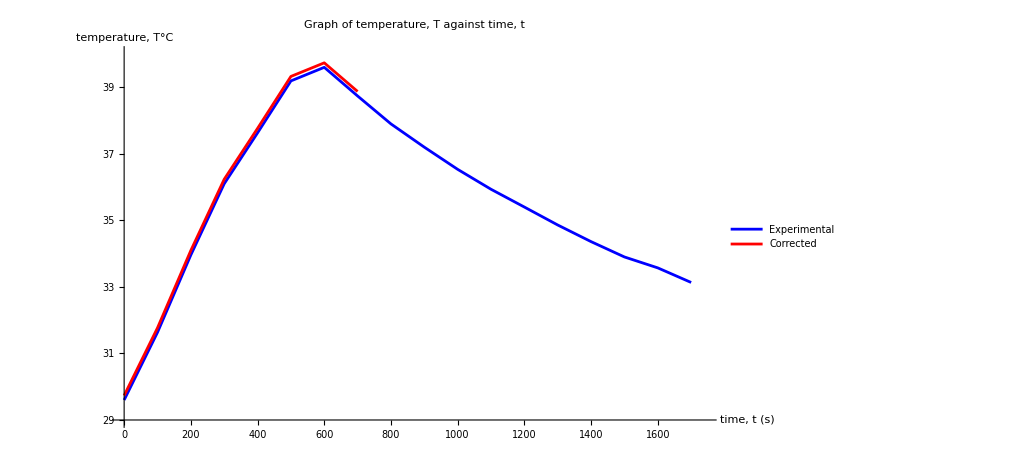

```mathematica
data={{0,29.6},{30,30.0},{60,30.7},{90,31.4},{120,32.1},{150,32.8},{180,33.5},{210,34.2},{240,35.0},{270,35.4},{300,36.1},{330,36.9},{360,37.0},{390,37.5},{420,37.9},{450,38.5},{480,39.0},{510,39.3},{540,39.9},{570,39.9},{600,39.6},{630,39.3},{660,39.0},{690,38.8},{720,38.6},{750,38.3},{780,38.1},{810,37.8},{840,37.6},{870,37.4},{900,37.2},{930,37.0},{960,36.8},{990,36.6},{1020,36.4},{1050,36.2},{1080,36.0},{1110,35.9},{1140,35.7},{1170,35.5},{1200,35.4},{1230,35.2},{1260,35.1},{1290,34.9},{1320,34.8},{1350,34.7},{1380,34.5},{1410,34.3},{1440,34.2},{1470,34.1},{1500,33.9},{1530,33.8},{1560,33.7},{1590,33.6},{1620,33.5},{1650,33.3},{1680,33.2},{1710,33.1},{1740,33.0}};

data2 ={{0,29.6+0.135},{30,30.0+0.135},{60,30.7+0.135},{90,31.4+0.135},{120,32.1+0.135},{150,32.8+0.135},{180,33.5+0.135},{210,34.2+0.135},{240,35.0+0.135},{270,35.4+0.135},{300,36.1+0.135},{330,36.9+0.135},{360,37.0+0.135},{390,37.5+0.135},{420,37.9+0.135},{450,38.5+0.135},{480,39.0+0.135},{510,39.3+0.135},{540,39.9+0.135},{ 570,39.9+0.135},{600,39.6+0.135},{630,39.3+0.135},{660,39.0+0.135},{690,38.8+0.135},{720,38.6+0.135}};

(*Create interpolation functions*)smoothCurve=Interpolation[data];
smoothCurve2=Interpolation[data2];

(*Generate and plot the interpolated data*)ListLinePlot[{Table[{x,smoothCurve[x]},{x,0,1740,100}],Table[{x,smoothCurve2[x]},{x,0,700,100}]},PlotLegends->{"Experimental","Corrected"},PlotStyle->{Blue,Red},AxesLabel->{"time, t (s)","temperature, T°C"},PlotLabel->"Graph of temperature, T against time, t",PlotRange->{{0,1740},{29,40}},Ticks->{{#,NumberForm[#,{3,1}]}&/@Range[0,1740,100],{#,NumberForm[#,{3,1}]}&/@Range[29,40,1]}]
```